### CKM Parameters

```mathematica
VudPDG=0.97373;
σVudPDG=0.00031;

VusPDG=0.2243;
σVusPDG=0.0008;

VcdPDG=0.221;
σVcdPDG=0.004;

VcsPDG=0.975;
σVcsPDG=0.006;

VcbPDG=40.8 10^-3;
σVcbPDG=1.4 10^-3;

VubPDG=3.82 10^-3;
σVubPDG=0.20 10^-3

VudSQPDG=VudPDG^2;
VusSQPDG=VusPDG^2;
VcdSQPDG=VcdPDG^2;
VcsSQPDG=VcsPDG^2;
VcbSQPDG=VcbPDG^2;
VubSQPDG=VubPDG^2;
```

0.0002

### Reading File

```mathematica
SetDirectory[NotebookDirectory[]];
NReplicas=40;
NBinsx=21;
NBinsQ2=12;
xBins=Table[N[10^i],{i,-3,0,3/NBinsx}];
Q2Bins=Table[N[10^i],{i,0,4,4/NBinsQ2}];

FileBinsxQ2[d]=Import["bins_xQ2_d.txt","Table"];

σBins[d,0]=FileBinsxQ2[d][[2;;NBinsQ2+1]];

For[iReplica=1,iReplica<=NReplicas,iReplica++,
σBins[d,iReplica]=FileBinsxQ2[d][[2+iReplica*(NBinsQ2+1);;(iReplica+1)*(NBinsQ2+1)]];];

FileBinsxQ2[s]=Import["bins_xQ2_s.txt","Table"];

σBins[s,0]=FileBinsxQ2[s][[2;;NBinsQ2+1]];

For[iReplica=1,iReplica<=NReplicas,iReplica++,
σBins[s,iReplica]=FileBinsxQ2[s][[2+iReplica*(NBinsQ2+1);;(iReplica+1)*(NBinsQ2+1)]];];

FileBinsxQ2[ub]=Import["bins_xQ2_ub.txt","Table"];

σBins[ub,0]=FileBinsxQ2[ub][[2;;NBinsQ2+1]];
	
For[iReplica=1,iReplica<=NReplicas,iReplica++,
σBins[ub,iReplica]=FileBinsxQ2[ub][[2+iReplica*(NBinsQ2+1);;(iReplica+1)*(NBinsQ2+1)]];];


FileBinsxQ2[cb]=Import["bins_xQ2_cb.txt","Table"];

σBins[cb,0]=FileBinsxQ2[cb][[2;;NBinsQ2+1]];
{21,12}
For[iReplica=1,iReplica<=NReplicas,iReplica++,
σBins[cb,iReplica]=FileBinsxQ2[cb][[2+iReplica*(NBinsQ2+1);;(iReplica+1)*(NBinsQ2+1)]];];
For[iReplica=0,iReplica<41, iReplica++,
σBins[d,iReplica] = Flatten[σBins[d,iReplica]];
σBins[s,iReplica] = Flatten[σBins[s,iReplica]];
σBins[ub,iReplica] = Flatten[σBins[ub,iReplica]];
σBins[cb,iReplica] = Flatten[σBins[cb,iReplica]];
]
```

{21,12}

### Filtering

```mathematica
posizioniDaRimuovere =#+1&/@{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,41,42,43,44,45,62,63,64,65,66,67,83,84,85,86,87,88,89,90,104,105,106,107,108,109,110,111,112,113,125,126,127,128,129,130,131,132,133,134,135,136,146,147,148,149,150,151,152,153,154,155,156,157,158,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251};

For[iReplica=0,iReplica<41, iReplica++,
σBins[d,iReplica]=Delete[σBins[d,iReplica],List/@posizioniDaRimuovere];
σBins[s,iReplica]=Delete[σBins[s,iReplica],List/@posizioniDaRimuovere];
σBins[ub,iReplica]=Delete[σBins[ub,iReplica],List/@posizioniDaRimuovere];
σBins[cb,iReplica]=Delete[σBins[cb,iReplica],List/@posizioniDaRimuovere];
]
```

### Cross Section

```mathematica
For[iReplica=0,iReplica<=NReplicas,iReplica++,
σBinsInclusive[iReplica][VcdSQ_,VcsSQ_]=
(VudSQPDG+VcdSQ)σBins[d,iReplica]+
(VusSQPDG+VcsSQ)σBins[s,iReplica]+
(VudSQPDG+VusSQPDG+VubSQPDG)σBins[ub,iReplica]+
(VcdSQ+VcsSQ+VcbSQPDG)σBins[cb,iReplica]/.Indeterminate->0;

σBinsInclusivePDG[iReplica]=
(VudSQPDG+VcdSQPDG)σBins[d,iReplica]+
(VusSQPDG+VcsSQPDG)σBins[s,iReplica]+
(VudSQPDG+VusSQPDG+VubSQPDG)σBins[ub,iReplica]+
(VcdSQPDG+VcsSQPDG+VcbSQPDG)σBins[cb,iReplica];

σBinsCtag[iReplica][VcdSQ_,VcsSQ_]=
VcdSQ σBins[d,iReplica]+VcsSQ σBins[s,iReplica];

σBinsCtagPDG[iReplica]=
VcdSQPDG σBins[d,iReplica]+VcsSQPDG σBins[s,iReplica];

Rreplicas[iReplica][VcdSQ_,VcsSQ_]=(σBinsCtag[iReplica][VcdSQ,VcsSQ]+σBinsCtag[0][VcdSQ,VcsSQ])/(σBinsInclusive[iReplica][VcdSQ,VcsSQ]+σBinsInclusive[0][VcdSQ,VcsSQ])/.Indeterminate->0;

RreplicasPDG[iReplica]=(σBinsCtagPDG[iReplica]+σBinsCtagPDG[0])/(σBinsInclusivePDG[iReplica]+σBinsInclusivePDG[0])/.Indeterminate->0;
]
```

### Chi2

```mathematica
λVar=Table[λ[[i]],{i,1,NReplicas}];
Rfunc[VcdSQ_,VcsSQ_,λ_]:=Rreplicas[0][VcdSQ,VcsSQ]+Sum[λ[[iReplica]](Rreplicas[iReplica][VcdSQ,VcsSQ]-Rreplicas[0][VcdSQ,VcsSQ]),{iReplica,1,NReplicas}];
RfuncPDG[λ_]:=Rfunc[VcdSQPDG,VcsSQPDG,λ];
```

Part::partd: Part specification λ⟦1⟧ is longer than depth of object.

Part::partd: Part specification λ⟦2⟧ is longer than depth of object.

Part::partd: Part specification λ⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Nνyear=6 10^16;
Nyears=5;
NA=6.022 10^23;
pbtocm2=10^-36;
ρL=5000;
Lumi=pbtocm2 NA ρL Nνyear Nyears
NctagBins=Lumi σBinsCtagPDG[0];
NInclusiveBins=Lumi σBinsInclusivePDG[0];
σstatR=RreplicasPDG[0] √(1/NctagBins+1/NInclusiveBins)/.{Indeterminate->10^6};
λZero=Table[0,{iReplica,1,NReplicas}];
```

9.033×10^8

```mathematica
χSQnoPDF[VcdSQ_,VcsSQ_]=Sum[((Rfunc[VcdSQ,VcsSQ,λZero][[i]]-RreplicasPDG[0][[i]])/σstatR[[i]])^2,{i,1,Length[σBins[d,0]]}]//Expand;
```

```mathematica
χSQnoPDF[0.22000^2,0.97200^2]
```

28766.9

```mathematica
λZero=Table[0,{iReplica,1,NReplicas}];
```

```mathematica
χSQ[VcdSQ_,VcsSQ_,λ_]:=Sum[((Rfunc[VcdSQ,VcsSQ,λ][[i]]-RreplicasPDG[0][[i]])/σstatR[[i]])^2,{i,1,Length[σBins[d,0]]}]+Sum[λ[[iReplica]]^2,{iReplica,1,NReplicas}];
```

```mathematica
χSQ[0.22100^2,0.97500^2,Table[10^-4,40]]
```

1.45528

```mathematica
FindMinimum[χSQ[0.22822^2,0.95702^2,λ],{λ,λZero}]
```

Part::partd: Part specification λ⟦1⟧ is longer than depth of object.

Part::partd: Part specification λ⟦2⟧ is longer than depth of object.

Part::partd: Part specification λ⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{19.5509,{λ→{0.0663441,0.0795546,-0.0819853,0.497294,0.538876,0.233081,-0.311014,0.0865778,-0.470602,-0.809075,0.431887,0.22144,0.0120076,-0.130291,-0.194402,0.103496,-0.61748,-0.052641,0.283286,-0.49077,0.669256,0.393124,-0.263177,0.325943,-0.266016,0.0573401,0.158105,0.0859927,0.161805,0.0908446,0.00780748,-0.133329,-0.178998,-0.172934,0.71318,0.422022,0.196875,-0.159956,0.219027,-0.105156}}}

```mathematica
RfuncFull[VcdSQ_,VcsSQ_,λ_]:=Rreplicas[0][VcdSQ,VcsSQ]+Sum[λ[[iReplica]]( σBinsCtag[iReplica][VcdSQ,VcsSQ]/σBinsInclusive[0][VcdSQ,VcsSQ] - σBinsInclusive[iReplica][VcdSQ,VcsSQ]σBinsCtag[0][VcdSQ,VcsSQ]/σBinsInclusive[0][VcdSQ,VcsSQ]^2),{iReplica,1,NReplicas}];
RfuncFullPDG[λ_]:=Rfunc[VcdSQPDG,VcsSQPDG,λ];

χSQFull[VcdSQ_,VcsSQ_,λ_]:=Sum[((RfuncFull[VcdSQ,VcsSQ,λ][[i]]-RreplicasPDG[0][[i]])/σstatR[[i]])^2,{i,1,Length[σBins[d,0]]}]+Sum[λ[[iReplica]]^2,{iReplica,1,NReplicas}];
```

```mathematica
FindMinimum[χSQFull[0.22822^2,0.95702^2,λ],{λ,λZero}]
```

Part::partd: Part specification λ⟦1⟧ is longer than depth of object.

Part::partd: Part specification λ⟦2⟧ is longer than depth of object.

Part::partd: Part specification λ⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{19.4107,{λ→{0.0306663,0.0801493,-0.111786,0.526007,0.528154,0.231662,-0.303996,0.116375,-0.442226,-0.799658,0.473204,0.273661,-0.0290708,-0.183856,-0.177551,0.120485,-0.61781,-0.0614112,0.321934,-0.480498,0.604593,0.374721,-0.272344,0.25862,-0.247085,0.122152,0.159371,0.0592928,0.160792,0.130574,0.0659339,-0.11038,-0.124587,-0.230044,0.750611,0.421059,0.172428,-0.114154,0.226558,-0.0931758}}}

```mathematica
(*Vcdpoints=Table[δ,{δ,0.21,0.235, 0.005}];
Vcspoints=Table[δ,{δ,0.96,0.99,0.005}];*)

Vcdpoints=Table[δ,{δ,0.21,0.23, 0.002}];
Vcspoints=Table[δ,{δ,0.96,0.99,0.003}];

Length[Vcdpoints]
Length[Vcspoints]

(*Esegui la minimizzazione per ogni combinazione di punti e stampa il valore*)results=Table[Module[{minResult},minResult=FindMinimum[χSQ[Vcdpoints[[i]]^2,Vcspoints[[j]]^2,λ],{λ,λZero}];
(*Stampa il valore minimo per ogni combinazione di punti*)Print["VcdSQ = ",Vcdpoints[[i]],", VcsSQ = ",Vcspoints[[j]]," -> Chi-Square Minimo = ",minResult[[1]]];
{Vcdpoints[[i]],Vcspoints[[j]],minResult[[1]]}  (*Restituisci i valori di VcdSQ,VcsSQ e il valore minimo della funzione*)],{i,1,Length[Vcdpoints]},{j,1,Length[Vcspoints]}];

(*Estrai i valori di VcdSQ,VcsSQ e il valore minimo della funzione*)
data=Flatten[results,1];  (*Appiattisci la lista per renderla più comoda per il plot*)

(*Creare il contour plot*)
```

VcdSQ = 0.21, VcsSQ = 0.99 -> Chi-Square Minimo = 18.9472

VcdSQ = 0.212, VcsSQ = 0.96 -> Chi-Square Minimo = 22.2183

VcdSQ = 0.212, VcsSQ = 0.963 -> Chi-Square Minimo = 17.2574

VcdSQ = 0.212, VcsSQ = 0.966 -> Chi-Square Minimo = 13.2693

VcdSQ = 0.212, VcsSQ = 0.969 -> Chi-Square Minimo = 10.2524

VcdSQ = 0.212, VcsSQ = 0.972 -> Chi-Square Minimo = 8.20497

VcdSQ = 0.212, VcsSQ = 0.975 -> Chi-Square Minimo = 7.12558

VcdSQ = 0.212, VcsSQ = 0.978 -> Chi-Square Minimo = 7.01272

VcdSQ = 0.212, VcsSQ = 0.981 -> Chi-Square Minimo = 7.86499

VcdSQ = 0.212, VcsSQ = 0.984 -> Chi-Square Minimo = 9.68105

VcdSQ = 0.212, VcsSQ = 0.987 -> Chi-Square Minimo = 12.4596

VcdSQ = 0.212, VcsSQ = 0.99 -> Chi-Square Minimo = 16.1995

VcdSQ = 0.214, VcsSQ = 0.96 -> Chi-Square Minimo = 18.7517

VcdSQ = 0.214, VcsSQ = 0.963 -> Chi-Square Minimo = 13.9303

VcdSQ = 0.214, VcsSQ = 0.966 -> Chi-Square Minimo = 10.0809

VcdSQ = 0.214, VcsSQ = 0.969 -> Chi-Square Minimo = 7.2019

VcdSQ = 0.214, VcsSQ = 0.972 -> Chi-Square Minimo = 5.2916

VcdSQ = 0.214, VcsSQ = 0.975 -> Chi-Square Minimo = 4.34848

VcdSQ = 0.214, VcsSQ = 0.978 -> Chi-Square Minimo = 4.37108

VcdSQ = 0.214, VcsSQ = 0.981 -> Chi-Square Minimo = 5.35798

VcdSQ = 0.214, VcsSQ = 0.984 -> Chi-Square Minimo = 7.30782

VcdSQ = 0.214, VcsSQ = 0.987 -> Chi-Square Minimo = 10.2193

VcdSQ = 0.214, VcsSQ = 0.99 -> Chi-Square Minimo = 14.0913

VcdSQ = 0.216, VcsSQ = 0.96 -> Chi-Square Minimo = 15.9616

VcdSQ = 0.216, VcsSQ = 0.963 -> Chi-Square Minimo = 11.2777

VcdSQ = 0.216, VcsSQ = 0.966 -> Chi-Square Minimo = 7.56501

VcdSQ = 0.216, VcsSQ = 0.969 -> Chi-Square Minimo = 4.82192

VcdSQ = 0.216, VcsSQ = 0.972 -> Chi-Square Minimo = 3.04679

VcdSQ = 0.216, VcsSQ = 0.975 -> Chi-Square Minimo = 2.23804

VcdSQ = 0.216, VcsSQ = 0.978 -> Chi-Square Minimo = 2.39421

VcdSQ = 0.216, VcsSQ = 0.981 -> Chi-Square Minimo = 3.51386

VcdSQ = 0.216, VcsSQ = 0.984 -> Chi-Square Minimo = 5.59562

VcdSQ = 0.216, VcsSQ = 0.987 -> Chi-Square Minimo = 8.63822

VcdSQ = 0.216, VcsSQ = 0.99 -> Chi-Square Minimo = 12.6404

VcdSQ = 0.218, VcsSQ = 0.96 -> Chi-Square Minimo = 13.8667

VcdSQ = 0.218, VcsSQ = 0.963 -> Chi-Square Minimo = 9.31824

VcdSQ = 0.218, VcsSQ = 0.966 -> Chi-Square Minimo = 5.74025

VcdSQ = 0.218, VcsSQ = 0.969 -> Chi-Square Minimo = 3.13107

VcdSQ = 0.218, VcsSQ = 0.972 -> Chi-Square Minimo = 1.48908

VcdSQ = 0.218, VcsSQ = 0.975 -> Chi-Square Minimo = 0.812715

VcdSQ = 0.218, VcsSQ = 0.978 -> Chi-Square Minimo = 1.10047

VcdSQ = 0.218, VcsSQ = 0.981 -> Chi-Square Minimo = 2.35091

VcdSQ = 0.218, VcsSQ = 0.984 -> Chi-Square Minimo = 4.56267

VcdSQ = 0.218, VcsSQ = 0.987 -> Chi-Square Minimo = 7.73444

VcdSQ = 0.218, VcsSQ = 0.99 -> Chi-Square Minimo = 11.865

VcdSQ = 0.22, VcsSQ = 0.96 -> Chi-Square Minimo = 12.4862

VcdSQ = 0.22, VcsSQ = 0.963 -> Chi-Square Minimo = 8.07097

VcdSQ = 0.22, VcsSQ = 0.966 -> Chi-Square Minimo = 4.6255

VcdSQ = 0.22, VcsSQ = 0.969 -> Chi-Square Minimo = 2.14811

VcdSQ = 0.22, VcsSQ = 0.972 -> Chi-Square Minimo = 0.637162

VcdSQ = 0.22, VcsSQ = 0.975 -> Chi-Square Minimo = 0.0910843

VcdSQ = 0.22, VcsSQ = 0.978 -> Chi-Square Minimo = 0.508366

VcdSQ = 0.22, VcsSQ = 0.981 -> Chi-Square Minimo = 1.88756

VcdSQ = 0.22, VcsSQ = 0.984 -> Chi-Square Minimo = 4.22729

VcdSQ = 0.22, VcsSQ = 0.987 -> Chi-Square Minimo = 7.52624

VcdSQ = 0.22, VcsSQ = 0.99 -> Chi-Square Minimo = 11.7831

VcdSQ = 0.222, VcsSQ = 0.96 -> Chi-Square Minimo = 11.8392

VcdSQ = 0.222, VcsSQ = 0.963 -> Chi-Square Minimo = 7.55492

VcdSQ = 0.222, VcsSQ = 0.966 -> Chi-Square Minimo = 4.23973

VcdSQ = 0.222, VcsSQ = 0.969 -> Chi-Square Minimo = 1.89192

VcdSQ = 0.222, VcsSQ = 0.972 -> Chi-Square Minimo = 0.509825

VcdSQ = 0.222, VcsSQ = 0.975 -> Chi-Square Minimo = 0.0918696

VcdSQ = 0.222, VcsSQ = 0.978 -> Chi-Square Minimo = 0.636532

VcdSQ = 0.222, VcsSQ = 0.981 -> Chi-Square Minimo = 2.14236

VcdSQ = 0.222, VcsSQ = 0.984 -> Chi-Square Minimo = 4.60795

VcdSQ = 0.222, VcsSQ = 0.987 -> Chi-Square Minimo = 8.03199

VcdSQ = 0.222, VcsSQ = 0.99 -> Chi-Square Minimo = 12.4132

VcdSQ = 0.224, VcsSQ = 0.96 -> Chi-Square Minimo = 11.9449

VcdSQ = 0.224, VcsSQ = 0.963 -> Chi-Square Minimo = 7.78929

VcdSQ = 0.224, VcsSQ = 0.966 -> Chi-Square Minimo = 4.60207

VcdSQ = 0.224, VcsSQ = 0.969 -> Chi-Square Minimo = 2.38152

VcdSQ = 0.224, VcsSQ = 0.972 -> Chi-Square Minimo = 1.12601

VcdSQ = 0.224, VcsSQ = 0.975 -> Chi-Square Minimo = 0.833918

VcdSQ = 0.224, VcsSQ = 0.978 -> Chi-Square Minimo = 1.50373

VcdSQ = 0.224, VcsSQ = 0.981 -> Chi-Square Minimo = 3.13397

VcdSQ = 0.224, VcsSQ = 0.984 -> Chi-Square Minimo = 5.72324

VcdSQ = 0.224, VcsSQ = 0.987 -> Chi-Square Minimo = 9.27021

VcdSQ = 0.224, VcsSQ = 0.99 -> Chi-Square Minimo = 13.7736

VcdSQ = 0.226, VcsSQ = 0.96 -> Chi-Square Minimo = 12.8228

VcdSQ = 0.226, VcsSQ = 0.963 -> Chi-Square Minimo = 8.79342

VcdSQ = 0.226, VcsSQ = 0.966 -> Chi-Square Minimo = 5.73174

VcdSQ = 0.226, VcsSQ = 0.969 -> Chi-Square Minimo = 3.63608

VcdSQ = 0.226, VcsSQ = 0.972 -> Chi-Square Minimo = 2.50477

VcdSQ = 0.226, VcsSQ = 0.975 -> Chi-Square Minimo = 2.3362

VcdSQ = 0.226, VcsSQ = 0.978 -> Chi-Square Minimo = 3.12884

VcdSQ = 0.226, VcsSQ = 0.981 -> Chi-Square Minimo = 4.88121

VcdSQ = 0.226, VcsSQ = 0.984 -> Chi-Square Minimo = 7.59188

VcdSQ = 0.226, VcsSQ = 0.987 -> Chi-Square Minimo = 11.2595

VcdSQ = 0.226, VcsSQ = 0.99 -> Chi-Square Minimo = 15.8828

VcdSQ = 0.228, VcsSQ = 0.96 -> Chi-Square Minimo = 14.4925

VcdSQ = 0.228, VcsSQ = 0.963 -> Chi-Square Minimo = 10.5868

VcdSQ = 0.228, VcsSQ = 0.966 -> Chi-Square Minimo = 7.64811

VcdSQ = 0.228, VcsSQ = 0.969 -> Chi-Square Minimo = 5.67486

VcdSQ = 0.228, VcsSQ = 0.972 -> Chi-Square Minimo = 4.6653

VcdSQ = 0.228, VcsSQ = 0.975 -> Chi-Square Minimo = 4.61783

VcdSQ = 0.228, VcsSQ = 0.978 -> Chi-Square Minimo = 5.53089

VcdSQ = 0.228, VcsSQ = 0.981 -> Chi-Square Minimo = 7.40299

VcdSQ = 0.228, VcsSQ = 0.984 -> Chi-Square Minimo = 10.2327

VcdSQ = 0.228, VcsSQ = 0.987 -> Chi-Square Minimo = 14.0187

VcdSQ = 0.228, VcsSQ = 0.99 -> Chi-Square Minimo = 18.7596

VcdSQ = 0.23, VcsSQ = 0.96 -> Chi-Square Minimo = 16.9736

VcdSQ = 0.23, VcsSQ = 0.963 -> Chi-Square Minimo = 13.1889

VcdSQ = 0.23, VcsSQ = 0.966 -> Chi-Square Minimo = 10.3707

VcdSQ = 0.23, VcsSQ = 0.969 -> Chi-Square Minimo = 8.51726

VcdSQ = 0.23, VcsSQ = 0.972 -> Chi-Square Minimo = 7.62691

VcdSQ = 0.23, VcsSQ = 0.975 -> Chi-Square Minimo = 7.69801

VcdSQ = 0.23, VcsSQ = 0.978 -> Chi-Square Minimo = 8.729

VcdSQ = 0.23, VcsSQ = 0.981 -> Chi-Square Minimo = 10.7184

VcdSQ = 0.23, VcsSQ = 0.984 -> Chi-Square Minimo = 13.6647

VcdSQ = 0.23, VcsSQ = 0.987 -> Chi-Square Minimo = 17.5666

VcdSQ = 0.23, VcsSQ = 0.99 -> Chi-Square Minimo = 22.4227

11

11

Part::partd: Part specification λ⟦1⟧ is longer than depth of object.

Part::partd: Part specification λ⟦2⟧ is longer than depth of object.

Part::partd: Part specification λ⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

VcdSQ = 0.21, VcsSQ = 0.96 -> Chi-Square Minimo = 26.3425

VcdSQ = 0.21, VcsSQ = 0.963 -> Chi-Square Minimo = 21.2402

VcdSQ = 0.21, VcsSQ = 0.966 -> Chi-Square Minimo = 17.1116

VcdSQ = 0.21, VcsSQ = 0.969 -> Chi-Square Minimo = 13.9549

VcdSQ = 0.21, VcsSQ = 0.972 -> Chi-Square Minimo = 11.7685

VcdSQ = 0.21, VcsSQ = 0.975 -> Chi-Square Minimo = 10.551

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

VcdSQ = 0.21, VcsSQ = 0.978 -> Chi-Square Minimo = 10.3009

VcdSQ = 0.21, VcsSQ = 0.981 -> Chi-Square Minimo = 11.0167

VcdSQ = 0.21, VcsSQ = 0.984 -> Chi-Square Minimo = 12.6972

VcdSQ = 0.21, VcsSQ = 0.987 -> Chi-Square Minimo = 15.3411

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

VcdSQ = 0.21, VcsSQ = 0.99 -> Chi-Square Minimo = 18.9472

VcdSQ = 0.212, VcsSQ = 0.96 -> Chi-Square Minimo = 22.2183

VcdSQ = 0.212, VcsSQ = 0.963 -> Chi-Square Minimo = 17.2574

VcdSQ = 0.212, VcsSQ = 0.966 -> Chi-Square Minimo = 13.2693

VcdSQ = 0.212, VcsSQ = 0.969 -> Chi-Square Minimo = 10.2524

VcdSQ = 0.212, VcsSQ = 0.972 -> Chi-Square Minimo = 8.20497

VcdSQ = 0.212, VcsSQ = 0.975 -> Chi-Square Minimo = 7.12558

VcdSQ = 0.212, VcsSQ = 0.978 -> Chi-Square Minimo = 7.01272

VcdSQ = 0.212, VcsSQ = 0.981 -> Chi-Square Minimo = 7.86499

VcdSQ = 0.212, VcsSQ = 0.984 -> Chi-Square Minimo = 9.68105

VcdSQ = 0.212, VcsSQ = 0.987 -> Chi-Square Minimo = 12.4596

VcdSQ = 0.212, VcsSQ = 0.99 -> Chi-Square Minimo = 16.1995

VcdSQ = 0.214, VcsSQ = 0.96 -> Chi-Square Minimo = 18.7517

VcdSQ = 0.214, VcsSQ = 0.963 -> Chi-Square Minimo = 13.9303

VcdSQ = 0.214, VcsSQ = 0.966 -> Chi-Square Minimo = 10.0809

VcdSQ = 0.214, VcsSQ = 0.969 -> Chi-Square Minimo = 7.2019

VcdSQ = 0.214, VcsSQ = 0.972 -> Chi-Square Minimo = 5.2916

VcdSQ = 0.214, VcsSQ = 0.975 -> Chi-Square Minimo = 4.34848

VcdSQ = 0.214, VcsSQ = 0.978 -> Chi-Square Minimo = 4.37108

VcdSQ = 0.214, VcsSQ = 0.981 -> Chi-Square Minimo = 5.35798

VcdSQ = 0.214, VcsSQ = 0.984 -> Chi-Square Minimo = 7.30782

VcdSQ = 0.214, VcsSQ = 0.987 -> Chi-Square Minimo = 10.2193

VcdSQ = 0.214, VcsSQ = 0.99 -> Chi-Square Minimo = 14.0913

VcdSQ = 0.216, VcsSQ = 0.96 -> Chi-Square Minimo = 15.9616

VcdSQ = 0.216, VcsSQ = 0.963 -> Chi-Square Minimo = 11.2777

VcdSQ = 0.216, VcsSQ = 0.966 -> Chi-Square Minimo = 7.56501

VcdSQ = 0.216, VcsSQ = 0.969 -> Chi-Square Minimo = 4.82192

VcdSQ = 0.216, VcsSQ = 0.972 -> Chi-Square Minimo = 3.04679

VcdSQ = 0.216, VcsSQ = 0.975 -> Chi-Square Minimo = 2.23804

VcdSQ = 0.216, VcsSQ = 0.978 -> Chi-Square Minimo = 2.39421

VcdSQ = 0.216, VcsSQ = 0.981 -> Chi-Square Minimo = 3.51386

VcdSQ = 0.216, VcsSQ = 0.984 -> Chi-Square Minimo = 5.59562

VcdSQ = 0.216, VcsSQ = 0.987 -> Chi-Square Minimo = 8.63822

VcdSQ = 0.216, VcsSQ = 0.99 -> Chi-Square Minimo = 12.6404

VcdSQ = 0.218, VcsSQ = 0.96 -> Chi-Square Minimo = 13.8667

VcdSQ = 0.218, VcsSQ = 0.963 -> Chi-Square Minimo = 9.31824

VcdSQ = 0.218, VcsSQ = 0.966 -> Chi-Square Minimo = 5.74025

VcdSQ = 0.218, VcsSQ = 0.969 -> Chi-Square Minimo = 3.13107

VcdSQ = 0.218, VcsSQ = 0.972 -> Chi-Square Minimo = 1.48908

VcdSQ = 0.218, VcsSQ = 0.975 -> Chi-Square Minimo = 0.812715

VcdSQ = 0.218, VcsSQ = 0.978 -> Chi-Square Minimo = 1.10047

VcdSQ = 0.218, VcsSQ = 0.981 -> Chi-Square Minimo = 2.35091

VcdSQ = 0.218, VcsSQ = 0.984 -> Chi-Square Minimo = 4.56267

VcdSQ = 0.218, VcsSQ = 0.987 -> Chi-Square Minimo = 7.73444

VcdSQ = 0.218, VcsSQ = 0.99 -> Chi-Square Minimo = 11.865

VcdSQ = 0.22, VcsSQ = 0.96 -> Chi-Square Minimo = 12.4862

VcdSQ = 0.22, VcsSQ = 0.963 -> Chi-Square Minimo = 8.07097

VcdSQ = 0.22, VcsSQ = 0.966 -> Chi-Square Minimo = 4.6255

VcdSQ = 0.22, VcsSQ = 0.969 -> Chi-Square Minimo = 2.14811

VcdSQ = 0.22, VcsSQ = 0.972 -> Chi-Square Minimo = 0.637162

VcdSQ = 0.22, VcsSQ = 0.975 -> Chi-Square Minimo = 0.0910843

VcdSQ = 0.22, VcsSQ = 0.978 -> Chi-Square Minimo = 0.508366

VcdSQ = 0.22, VcsSQ = 0.981 -> Chi-Square Minimo = 1.88756

VcdSQ = 0.22, VcsSQ = 0.984 -> Chi-Square Minimo = 4.22729

VcdSQ = 0.22, VcsSQ = 0.987 -> Chi-Square Minimo = 7.52624

VcdSQ = 0.22, VcsSQ = 0.99 -> Chi-Square Minimo = 11.7831

VcdSQ = 0.222, VcsSQ = 0.96 -> Chi-Square Minimo = 11.8392

VcdSQ = 0.222, VcsSQ = 0.963 -> Chi-Square Minimo = 7.55492

VcdSQ = 0.222, VcsSQ = 0.966 -> Chi-Square Minimo = 4.23973

VcdSQ = 0.222, VcsSQ = 0.969 -> Chi-Square Minimo = 1.89192

VcdSQ = 0.222, VcsSQ = 0.972 -> Chi-Square Minimo = 0.509825

VcdSQ = 0.222, VcsSQ = 0.975 -> Chi-Square Minimo = 0.0918696

VcdSQ = 0.222, VcsSQ = 0.978 -> Chi-Square Minimo = 0.636532

VcdSQ = 0.222, VcsSQ = 0.981 -> Chi-Square Minimo = 2.14236

VcdSQ = 0.222, VcsSQ = 0.984 -> Chi-Square Minimo = 4.60795

VcdSQ = 0.222, VcsSQ = 0.987 -> Chi-Square Minimo = 8.03199

VcdSQ = 0.222, VcsSQ = 0.99 -> Chi-Square Minimo = 12.4132

VcdSQ = 0.224, VcsSQ = 0.96 -> Chi-Square Minimo = 11.9449

VcdSQ = 0.224, VcsSQ = 0.963 -> Chi-Square Minimo = 7.78929

VcdSQ = 0.224, VcsSQ = 0.966 -> Chi-Square Minimo = 4.60207

VcdSQ = 0.224, VcsSQ = 0.969 -> Chi-Square Minimo = 2.38152

VcdSQ = 0.224, VcsSQ = 0.972 -> Chi-Square Minimo = 1.12601

VcdSQ = 0.224, VcsSQ = 0.975 -> Chi-Square Minimo = 0.833918

VcdSQ = 0.224, VcsSQ = 0.978 -> Chi-Square Minimo = 1.50373

VcdSQ = 0.224, VcsSQ = 0.981 -> Chi-Square Minimo = 3.13397

VcdSQ = 0.224, VcsSQ = 0.984 -> Chi-Square Minimo = 5.72324

VcdSQ = 0.224, VcsSQ = 0.987 -> Chi-Square Minimo = 9.27021

VcdSQ = 0.224, VcsSQ = 0.99 -> Chi-Square Minimo = 13.7736

VcdSQ = 0.226, VcsSQ = 0.96 -> Chi-Square Minimo = 12.8228

VcdSQ = 0.226, VcsSQ = 0.963 -> Chi-Square Minimo = 8.79342

VcdSQ = 0.226, VcsSQ = 0.966 -> Chi-Square Minimo = 5.73174

VcdSQ = 0.226, VcsSQ = 0.969 -> Chi-Square Minimo = 3.63608

VcdSQ = 0.226, VcsSQ = 0.972 -> Chi-Square Minimo = 2.50477

VcdSQ = 0.226, VcsSQ = 0.975 -> Chi-Square Minimo = 2.3362

VcdSQ = 0.226, VcsSQ = 0.978 -> Chi-Square Minimo = 3.12884

VcdSQ = 0.226, VcsSQ = 0.981 -> Chi-Square Minimo = 4.88121

VcdSQ = 0.226, VcsSQ = 0.984 -> Chi-Square Minimo = 7.59188

VcdSQ = 0.226, VcsSQ = 0.987 -> Chi-Square Minimo = 11.2595

VcdSQ = 0.226, VcsSQ = 0.99 -> Chi-Square Minimo = 15.8828

VcdSQ = 0.228, VcsSQ = 0.96 -> Chi-Square Minimo = 14.4925

VcdSQ = 0.228, VcsSQ = 0.963 -> Chi-Square Minimo = 10.5868

VcdSQ = 0.228, VcsSQ = 0.966 -> Chi-Square Minimo = 7.64811

VcdSQ = 0.228, VcsSQ = 0.969 -> Chi-Square Minimo = 5.67486

VcdSQ = 0.228, VcsSQ = 0.972 -> Chi-Square Minimo = 4.6653

VcdSQ = 0.228, VcsSQ = 0.975 -> Chi-Square Minimo = 4.61783

VcdSQ = 0.228, VcsSQ = 0.978 -> Chi-Square Minimo = 5.53089

VcdSQ = 0.228, VcsSQ = 0.981 -> Chi-Square Minimo = 7.40299

VcdSQ = 0.228, VcsSQ = 0.984 -> Chi-Square Minimo = 10.2327

VcdSQ = 0.228, VcsSQ = 0.987 -> Chi-Square Minimo = 14.0187

VcdSQ = 0.228, VcsSQ = 0.99 -> Chi-Square Minimo = 18.7596

VcdSQ = 0.23, VcsSQ = 0.96 -> Chi-Square Minimo = 16.9736

VcdSQ = 0.23, VcsSQ = 0.963 -> Chi-Square Minimo = 13.1889

VcdSQ = 0.23, VcsSQ = 0.966 -> Chi-Square Minimo = 10.3707

VcdSQ = 0.23, VcsSQ = 0.969 -> Chi-Square Minimo = 8.51726

VcdSQ = 0.23, VcsSQ = 0.972 -> Chi-Square Minimo = 7.62691

VcdSQ = 0.23, VcsSQ = 0.975 -> Chi-Square Minimo = 7.69801

VcdSQ = 0.23, VcsSQ = 0.978 -> Chi-Square Minimo = 8.729

VcdSQ = 0.23, VcsSQ = 0.981 -> Chi-Square Minimo = 10.7184

VcdSQ = 0.23, VcsSQ = 0.984 -> Chi-Square Minimo = 13.6647

VcdSQ = 0.23, VcsSQ = 0.987 -> Chi-Square Minimo = 17.5666

VcdSQ = 0.23, VcsSQ = 0.99 -> Chi-Square Minimo = 22.4227

VcdSQ = 0.21, VcsSQ = 0.963 -> Chi-Square Minimo = 512120.

VcdSQ = 0.21, VcsSQ = 0.966 -> Chi-Square Minimo = 414922.

$Aborted

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[results,1].

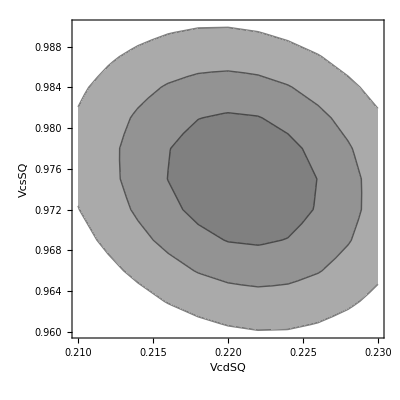

```mathematica
ListContourPlot[data,PlotRange->All,Contours->{2.28,5.99,11.62},AxesLabel->{"VcdSQ","VcsSQ"},ColorFunction->(Blend[{Gray, White},#]&)
,FrameLabel->{"VcdSQ","VcsSQ","Chi-Square"}]
```